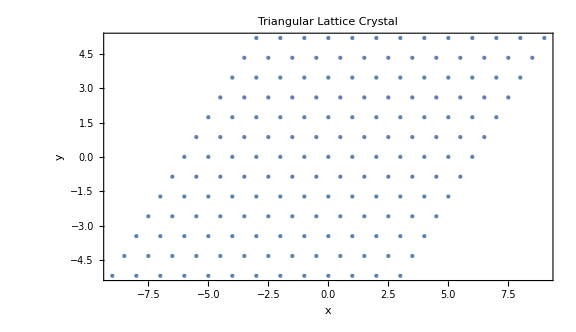

```mathematica
(* Define the lattice vector *)
A1={1,0}; 
A2={1/2,Sqrt[3]/2};
(* Number of lattice points in each direction *)
n=6; 
(* Lattice generation and visualization *)
TriX=Flatten[Table[A1*i+A2*j,{i,-n,n},{j,-n,n}],1];
plotLattice = ListPlot[TriX,AspectRatio->Automatic,PlotStyle->PointSize[Large],Frame->True,FrameLabel->{"x","y"},PlotLabel->"Triangular Lattice Crystal", ImageSize->Large]
```

```mathematica
(* Parameters *)
t=1;           (* Hopping strength *)
J = 5;          (* Hund's coupling strength *)
```

```mathematica
(* Spin texture implimentation - Triple Q state of SkX*)
(* direction vectors of each spin helix in superposition *)
basisVectors = {{1,0}, {-1/2,Sqrt[3]/2}, {-1/2, -Sqrt[3]/2}};
(* The reciprocal space lattice vectors *)
QVectors =  Pi/(3 * Sqrt[3]){{2 Sqrt[3], 0},{-Sqrt[3], 3},{-Sqrt[3], -3}};
(* Initail phase or epoch *)
epoch={Pi/3,Pi/3,Pi/3};
(* Spin texture *)
mxy [x_, y_] := Total[Table[(Sin[QVectors[[i]].{x,y}+epoch[[i]] ]) basisVectors[[i]],{i,1,3}]]
mz[x_, y_] :=  Total[Table[(Cos[QVectors[[i]].{x,y} +epoch[[i]]]),{i,1,3}]]
(* Spin texture function to get the 3D tuples *)
spins[x_, y_] := {N[mxy[x, y].{1,0}],N[ mxy[x, y].{0,1}], N[mz[x,y]]}
```

```mathematica
(* Visualization of the spin texture *)
(* Position vectors as 3D tuples *)
POSlist = Table[{TriX[[i]][[1]],TriX[[i]][[2]],0},{i,1,Length[TriX]}];
(* Generating the spin texture and normalizing them *)
texture =Table[spins[TriX[[i]][[1]], TriX[[i]][[2]]],{i, 1, Length[TriX]}]// N// Chop;
NORMtext = Table[texture[[i]]/Norm[texture[[i]]],{i,1,Length[texture]}];
(* Plotting the spin texture *)
cylinders = Table[
{{ColorData["Rainbow"][Rescale[NORMtext[[i]][[3]],{0,1}]],Cylinder[{POSlist[[i]]-NORMtext[[i]]/2,POSlist[[i]]},1/10]}},{i,1,Length[TriX] }];

cones= Table[
{{ColorData["Rainbow"][Rescale[NORMtext[[i]][[3]],{0,1}]],
Cone[{POSlist[[i]],POSlist[[i]]+NORMtext[[i]]/2},1/5]}},{i,1,Length[TriX] }];

texturePlot=Graphics3D[{cylinders,cones},Boxed->False,Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->All,  ImageSize->Full, Lighting->{{"Ambient",White}} ]
```

-Graphics3D-

```mathematica
(* Isolating single skyrmion position tuples *)
SkX = Table[If[Norm[TriX[[i]]]<=2, TriX[[i]]],{i, 1 , Length[TriX],1}];
SkX//MatrixForm;
UNITcell = DeleteCases[SkX,Null];
UNITcell // MatrixForm;
(* Getting the Unitcell tuples *)
For[i = 0,i<= 2,i++,
v = i *A1 + (2-i)*A2;
UNITcell = DeleteCases[UNITcell,v];
UNITcell= DeleteCases[UNITcell,{v[[1]], - v[[2]]}];
UNITcell = DeleteCases[UNITcell,{-i, - Sqrt[3]}];
] 
plotC1 = ListPlot[UNITcell,AspectRatio->Automatic,PlotStyle->PointSize[Large],Frame->True,FrameLabel->{"x","y"},PlotLabel->"Triangular Lattice Crystal"];


UNITcell= Table[UNITcell[[i]]+{-2,0},{i,1,Length[UNITcell]}];
plotC2 = ListPlot[UNITcell,AspectRatio->Automatic,PlotStyle->PointSize[Large],Frame->True,FrameLabel->{"x","y"},PlotLabel->"Triangular Lattice Crystal"];

(* Visualization of the isolated unitcell *)
OPvector = Table[{UNITcell[[i]][[1]],UNITcell[[i]][[2]],0},{i,1,Length[UNITcell]}];
sfield =Chop[N[Table[spins[UNITcell[[i]][[1]],UNITcell[[i]][[2]]],{i, 1, Length[UNITcell]}]]];
(* Spin texture in a unitcell *)
spinfield = Table[sfield[[i]]/Norm[sfield[[i]]],{i,1,Length[sfield]}];
cylinders1 = Table[
{{ColorData["Rainbow"][Rescale[spinfield[[i]][[3]],{0,1}]],Cylinder[{OPvector[[i]]-spinfield[[i]]/2,OPvector[[i]]},1/10]}},{i,1,Length[UNITcell] }
];
cones1= Table[
{{ColorData["Rainbow"][Rescale[spinfield[[i]][[3]],{0,1}]],
Cone[{OPvector[[i]],OPvector[[i]]+spinfield[[i]]/2},1/5]}},{i,1,Length[UNITcell] }
];
unitcellPLOT=Graphics3D[{cylinders1,cones1},Boxed->False,Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->All,  ImageSize->Small, Lighting->{{"Ambient",White}} ]
```

-Graphics3D-

```mathematica
(* Converting to Spherical Polar Coordinates *)
SpinPOLAR=CoordinateTransform["Cartesian"->"Spherical",spinfield]/.Indeterminate->0;
SpinPOLAR//MatrixForm;
SpinPOLAR = Table[If[SpinPOLAR[[i]][[3]]<0, {SpinPOLAR[[i]][[1]],SpinPOLAR[[i]][[2]],SpinPOLAR[[i]][[3]] + 2 Pi}, SpinPOLAR[[i]]],{i,1,Length[SpinPOLAR]}];
SpinPOLAR//MatrixForm
SpinPOLAR = Table[ {SpinPOLAR[[i]][[1]],SpinPOLAR[[i]][[2]],SpinPOLAR[[i]][[3]] +N[ Pi]},{i,1,Length[SpinPOLAR]}];
SpinPOLAR//MatrixForm
```

ArcTan::indet: Indeterminate expression ArcTan[0.,0.] encountered.

General::stop: Further output of ArcTan::indet will be suppressed during this calculation.

(1. | 0. | 0
1. | 0. | 0
1. | 0. | 0
1. | 0. | 0
1. | 1.85183 | 0.
1. | 1.85183 | 5.23599
1. | 0. | 0
1. | 1.85183 | 1.0472
1. | 3.14159 | 0
1. | 1.85183 | 4.18879
1. | 1.85183 | 2.0944
1. | 1.85183 | 3.14159)

(1. | 0. | 3.14159
1. | 0. | 3.14159
1. | 0. | 3.14159
1. | 0. | 3.14159
1. | 1.85183 | 3.14159
1. | 1.85183 | 8.37758
1. | 0. | 3.14159
1. | 1.85183 | 4.18879
1. | 3.14159 | 3.14159
1. | 1.85183 | 7.33038
1. | 1.85183 | 5.23599
1. | 1.85183 | 6.28319)

```mathematica
(* Collecting the theta and phi values *)
θ =Table[SpinPOLAR[[i]][[2]],{i,1,Length[SpinPOLAR]}];
ϕ =Table[SpinPOLAR[[i]][[3]],{i,1,Length[SpinPOLAR]}];
(* Neighbour table for Periodic Boundary condition Implimentation *)
NN1 = {5,6,7,8,9,10,1,11,12,4,2,3};
NN2 = {7,11,12,10,1,2,3,4,5,6,8,9};
NN3 = {2,3,8,5,6,7,11,9,10,1,12,4};
NN4 = {4,5,6,3,8,9,10,7,11,12,1,2};
NN5 = {11,12,4,1,2,3,8,5,6,7,9,10};
NN6 = {10,1,2,12,4,5,6,3,8,9,7,11};
```

```mathematica
KetArray = Table[{Cos[1/2 θ⟦i⟧], Sin[1/2 θ⟦i⟧] ⅇ^(ⅈ ϕ⟦i⟧)},{i,1,Length[SpinPOLAR]}]//Chop;
KetArray// MatrixForm;
(* The conjugate vector of the spin texture |χ⟩, ⟨χ|:=|χ⟩† *)
BraArray = Table[Conjugate[KetArray[[i]]],{i,1,Length[KetArray]}];
```

```mathematica
K[kx_, ky_] := {kx, ky}
(* Hamiltonian matrix *)
Hij[kx_, ky_, ras_] := Module[{hopingProduct},
hopingProduct = ConstantArray[0,{Length[SpinPOLAR],Length[SpinPOLAR]}];
For[i = 1, i<= Length[SpinPOLAR], i++,
hopingProduct[[i]][[NN1[[i]]]] =  t BraArray[[i]].KetArray[[NN1[[i]]]] ⅇ^(ⅈ K[kx,ky].{1,0})   +   ras*I* BraArray[[i]].(-PauliMatrix[2]).KetArray[[NN1[[i]]]] ⅇ^(ⅈ K[kx,ky].{1,0});

hopingProduct[[i]][[NN2[[i]]]] =  t BraArray[[i]].KetArray[[NN2[[i]]]] ⅇ^(ⅈ K[kx,ky].{-1,0}) +   ras*I* BraArray[[i]].(PauliMatrix[2]).KetArray[[NN2[[i]]]] ⅇ^(ⅈ K[kx,ky].{-1,0});

hopingProduct[[i]][[NN3[[i]]]] =t BraArray[[i]].KetArray[[NN3[[i]]]] ⅇ^(ⅈ K[kx,ky].{1/2,(√3)/2}) + ras*I* BraArray[[i]].((√3)/2 PauliMatrix[1] - 1/2 PauliMatrix[2] ).KetArray[[NN3[[i]]]] ⅇ^(ⅈ K[kx,ky].{1/2,(√3)/2}) ; 
hopingProduct[[i]][[NN4[[i]]]] =  t BraArray[[i]].KetArray[[NN4[[i]]]] ⅇ^(ⅈ K[kx,ky].{1/2,(-√3)/2})   +ras*I* BraArray[[i]].((-√3)/2 PauliMatrix[1] - 1/2 PauliMatrix[2] ).KetArray[[NN4[[i]]]] ⅇ^(ⅈ K[kx,ky].{1/2,(-√3)/2});
hopingProduct[[i]][[NN5[[i]]]] =  t BraArray[[i]].KetArray[[NN5[[i]]]] ⅇ^(ⅈ K[kx,ky].{-1/2,(√3)/2})   + ras*I* BraArray[[i]].((√3)/2 PauliMatrix[1] + 1/2 PauliMatrix[2] ).KetArray[[NN5[[i]]]] ⅇ^(ⅈ K[kx,ky].{-1/2,(√3)/2});
hopingProduct[[i]][[NN6[[i]]]] =  t BraArray[[i]].KetArray[[NN6[[i]]]] ⅇ^(ⅈ K[kx,ky].{-1/2,(-√3)/2})   +   ras*I* BraArray[[i]].((-√3)/2 PauliMatrix[1] + 1/2 PauliMatrix[2] ).KetArray[[NN6[[i]]]] ⅇ^(ⅈ K[kx,ky].{-1/2,(-√3)/2});
hopingProduct[[i]][[i]] = 0;];
hopingProduct
]
```

```mathematica
(* Eigenvalue function *)
Ev[kx_,ky_, ras_] := Sort[Eigenvalues[Hij[kx, ky, ras]] ]
(* Collection of Eigen values along the irreducible path in the reciprocal space *)
d=25; (* step count *)
tabGK[n_, ras_]:=Table[Ev[k,k/(√3),ras][[n]],{k,0, Pi/(3),Pi/(3 * d)}];
tabKM[n_, ras_]:=Table[Ev[π/3,ky,ras][[n]],{ky,Pi/(3 √3),0,-Pi/(3 √3*d)}];
tabMG[n_, ras_]:=Table[Ev[kx,0,ras][[n]],{kx,Pi/(3),0,-Pi/(3*0.87*d)}];
```

```mathematica
join[i_, ras_]:= Join[tabGK[i, ras],tabKM[i, ras],tabMG[i, ras]]
bands[ras_] := Table[join[i,ras],{i,1,Length[SpinPOLAR]}];
plotting[ras_]:=Show[ListLinePlot[bands[ras],ImageSize->Medium,AspectRatio->1,PlotRange->All,FrameTicks->{{Automatic,None},{customTicksX,None}},Axes->False,Frame->True,PlotLabel->"12 Site Skyrmion Model in Triangular Lattice",FrameTicksStyle->Directive[Bold,Black]], vl1, vl2];
```

```mathematica
(*Animation code*)
animation = Animate[Column[{plotting[rashba],Text["Rashba coupling: "<>ToString[rashba]]}],{{rashba,0,"Rashba strength"},-1,1,0.01},AnimationRunning->False]
```

```mathematica
alpha = Table[i,{i,-1,1,0.01}];
DataSet = Table[bands[rashba],{rashba,-1,1,0.01}];
```

```mathematica
BandWidth =Transpose[ Table[Abs[Max[Chop[DataSet[[i]][[bandindex]]]] -Min[ Chop[DataSet[[i]][[bandindex]]]]],{i,1,Length[DataSet]},{bandindex, 1, Length[SpinPOLAR]}]];
BandWidth//Dimensions
```

{12,201}

```mathematica
Data = Table[{alpha[[i]],BandWidth[[j]][[i]]},{j,1,Length[SpinPOLAR]},{i,1,Length[alpha]}];
```

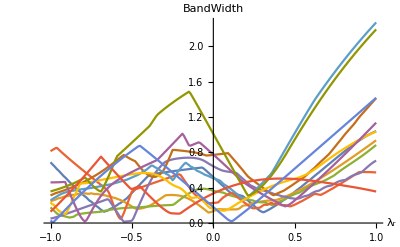

```mathematica
plots = Table[ListLinePlot[Data[[i]],PlotStyle->ColorData[97,i], AxesLabel->{"λ_r","BandWidth"}],{i,1,Length[SpinPOLAR]}];
Show[plots,PlotRange->All,BaseStyle->{FontSize->16}]
```